```mathematica
kmax=11;
weight=4/Sqrt[Pi]*Exp[-x^2]*x^2;
xmin = 0;
xmax = Infinity;
p=Array[0&,{kmax, 1}];p[[1]]=1;
np=Array[0&,{kmax, 1}];
an=Array[0&,{kmax, 1}];
mp=Array[0&,{kmax, 1}];
bn=Array[0&,{kmax, 1}];
For[k=1,k<=kmax,k=k+1,
If[k==2,p[[k]]=Simplify[(x-an[[k-1]])*p[[k-1]]]];
If[k>2,p[[k]]=Simplify[(x-an[[k-1]])*p[[k-1]]-bn[[k-1]]*p[[k-2]]]];
np[[k]]=NIntegrate[p[[k]]^2*weight,{x,xmin,xmax},WorkingPrecision->100,PrecisionGoal->90];
mp[[k]]=NIntegrate[x*p[[k]]^2*weight,{x,xmin,xmax},WorkingPrecision->100,PrecisionGoal->90];
an[[k]]=mp[[k]]/np[[k]];
If[k==1,bn[[k]]=np[[k]],bn[[k]]=np[[k]]/np[[k-1]]];
]
```

NIntegrate::precw: The precision of the argument function ((4 ⅇ^(-x^2) x^2 («135»-«135» x+x^2)^2)/(√π)) is less than WorkingPrecision (100.).

NIntegrate::precw: The precision of the argument function ((4 ⅇ^(-x^2) x^3 («135»-«135» x+x^2)^2)/(√π)) is less than WorkingPrecision (100.).

NIntegrate::precw: The precision of the argument function ((4 ⅇ^(-x^2) x^2 (-«135»+«135» x-«135» x^2+x^3)^2)/(√π)) is less than WorkingPrecision (100.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

```mathematica
For[k=2,k<=kmax,k=k+1,
p[[k]]=Simplify[p[[k]]/Sqrt[np[[k]]]];
]
```

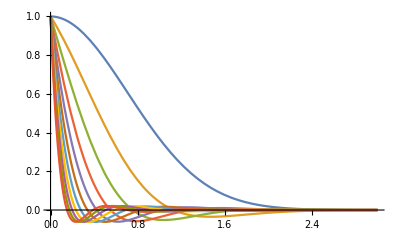

```mathematica
Plot[Evaluate[Table[Exp[-x^2]*HornerForm[N[p[[k]],32]]/(p[[k]]/.x->0),{k,1,kmax}]],{x,0,3}, PlotRange->All]
```

```mathematica
nodes=Array[0&,kmax*(kmax+1)/2];
gaussweights = Array[0&,kmax*(kmax+1)/2];
```

```mathematica
For[k=2,k≤kmax,k=k+1,J=DiagonalMatrix[an[[1;;k]]]+DiagonalMatrix[Sqrt[bn[[2;;k]]],1]+DiagonalMatrix[Sqrt[bn[[2;;k]]],-1];
nodes[[k*(k-1)/2+1;;k*(k-1)/2+k]]=Eigenvalues[N[J,32]];
For[i=1,i≤k,i=i+1,
pi=Evaluate[Table[HornerForm[N[p[[l]],32]],{l,1,k}]/.x->nodes[[k*(k-1)/2+i]]];
gaussweights[[k*(k-1)/2+i]]=1/(pi.pi);
]
]
```

```mathematica
ScientificForm[Grid[Transpose[{Flatten[CoefficientList[p,x]], nodes,gaussweights}]],16,NumberFormat->(Row[{#1,"e",If[#3≠"",#3,"0"]}]&)]
```

1e0 | 0e0 | 0e0
-2.369580128666418e0 | 1.734055298879163e0 | 3.820062585284651e-1
2.099985712041991e0 | 7.539869079898871e-1 | 6.179937414715349e-1
4.213816460538476e0 | 2.220484543409827e0 | 8.661475544173477e-2
-8.018748837448237e0 | 1.287309029870267e0 | 5.878737647484881e-1
3.222915115872983e0 | 5.507554932505808e-1 | 3.255114798097771e-1
-6.501995408801263e0 | 2.639813333635586e0 | 1.530823956791865e-2
1.978462372726331e1 | 1.742437375162050e0 | 2.624503955161513e-1
-1.676208550595413e1 | 1.014332104566760e0 | 5.496198376952335e-1
4.130068463181765e0 | 4.238628193900528e-1 | 1.726215272206965e-1
9.208093672644249e0 | 3.014172467490103e0 | 2.325848310677874e-3
-3.957498385244903e1 | 2.145408222421013e0 | 8.059849418234906e-2
5.276515502807088e1 | 1.432854372673354e0 | 3.910351060727549e-1
-2.710129697825156e1 | 8.266625437735953e-1 | 4.303885022636605e-1
4.656223713479861e0 | 3.384095960694548e-1 | 9.565204917055759e-2
-1.231169059573852e1 | 3.355569460485549e0 | 3.187008664128108e-4
6.968992827463914e1 | 2.510418043596144e0 | 1.964359119652011e-2
-1.294644384061650e2 | 1.813832458287184e0 | 1.789793538861901e-1
1.036384339043855e2 | 1.208987335897926e0 | 4.308814665589063e-1
-3.684587359785428e1 | 6.899111472440117e-1 | 3.144607240624743e-1
4.749705367508299e0 | 2.777894381395164e-1 | 5.571616342949640e-2
1.579642692591390e1 | 3.671425279510608e0 | 4.048448517191664e-5
-1.125356457463974e2 | 2.846250992174051e0 | 4.081185602865505e-3
2.721538070979604e2 | 2.164505782336081e0 | 6.202058417878846e-2
-3.010164693960598e2 | 1.566494333295838e0 | 2.678397210684480e-1
1.657233046675599e2 | 1.038409736727032e0 | 4.076441843458272e-1
-4.397864486190894e1 | 5.864425438286869e-1 | 2.243543980530160e-1
4.461889076846308e0 | 2.330573287335084e-1 | 3.401944226588289e-2
-1.964881336911186e1 | 3.966720403265353e0 | 4.851505118887007e-6
1.706121813389389e2 | 3.158780677105240e0 | 7.535209100793761e-4
-5.141239560322256e2 | 2.490479841967435e0 | 1.768220740785707e-2
7.348520149511671e2 | 1.900969572329702e0 | 1.225745652329119e-1
-5.558054532431382e2 | 1.372615723971598e0 | 3.225635969644352e-1
2.273566212114926e2 | 9.041682182040568e-1 | 3.551390337718458e-1
-4.730483875889135e1 | 5.059526450205794e-1 | 1.596192752254783e-1
3.907364039057229e0 | 1.990000637984294e-1 | 2.166294898227343e-2
2.385745012493591e1 | 4.244994854860493e0 | 5.549928329009120e-7
-2.465040056058034e2 | 3.452158053324797e0 | 1.269728038315379e-4
8.975634080863863e2 | 2.795977077890247e0 | 4.356868836404519e-3
-1.588283510512323e3 | 2.215244804617891e0 | 4.511577174838308e-2
1.544564973542812e3 | 1.690321564523553e0 | 1.849888689497515e-1
-8.644293027751230e2 | 1.216033402657007e0 | 3.410603163100898e-1
2.762853546117040e2 | 7.960713739444719e-1 | 2.956593043080275e-1
-4.666402014811854e1 | 4.419446984218556e-1 | 1.143802965887825e-1
3.218499694441584e0 | 1.723990735308230e-1 | 1.431104546189666e-2
-2.841251201909715e1 | 4.508873956661538e0 | 6.112029882496220e-8
3.428725145179459e2 | 3.729441985537364e0 | 1.988531894560531e-5
-1.474430608575566e3 | 3.084208876618047e0 | 9.578663217570229e-4
3.134660665086940e3 | 2.512001841975460e0 | 1.408320926248684e-2
-3.756914723639971e3 | 1.992083005155480e0 | 8.412939588639322e-2
2.693368681388479e3 | 1.517073815957226e0 | 2.355752093078595e-1
-1.174103579166501e3 | 1.086935487983822e0 | 3.323427698323715e-1
3.038084069768712e2 | 7.074718987907389e-1 | 2.401949234927424e-1
-4.274719050716197e1 | 3.901088173894345e-1 | 8.293498273107983e-2
2.510826824016828e0 | 1.511749584213949e-1 | 9.761696726065352e-3
3.330539677160998e1 | 4.760369583820472e0 | 6.520548141201987e-9
-4.624499119544574e2 | 3.992961725191356e0 | 2.932414612998732e-6
2.307301153119034e3 | 3.357661775834936e0 | 1.920863463637292e-4
-5.763852633976373e3 | 2.793533584496316e0 | 3.860543167387789e-3
8.265842267005106e3 | 2.279227538234959e0 | 3.204309817297811e-2
-7.278670999315705e3 | 1.806061016164994e0 | 1.279869774191817e-1
4.052921960948740e3 | 1.371796161185106e0 | 2.680318755015593e-1
-1.426858758983212e3 | 9.788300256746094e-1 | 3.072815415615890e-1
3.069237592694729e2 | 6.337976010969141e-1 | 1.927905456828253e-1
-3.670772659772201e1 | 3.474769547766709e-1 | 6.096343397482035e-2
1.865289281842033e0 | 1.339333135146753e-1 | 6.846959238133618e-3

```mathematica
testpoly=x^18;q=10;
Integrate[testpoly*weight,{x,xmin,xmax}]-(testpoly/.x->nodes[[q*(q-1)/2+1;;q*(q-1)/2+q]]).gaussweights[[q*(q-1)/2+1;;q*(q-1)/2+q]]
```

0.

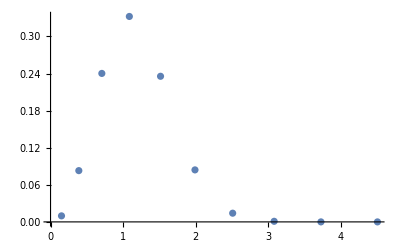

```mathematica
ListPlot[Transpose[{nodes[[q*(q-1)/2+1;;q*(q-1)/2+q]],gaussweights[[q*(q-1)/2+1;;q*(q-1)/2+q]]}]]
```

```mathematica
testf=(1.2+Cos[2*x+1.75])*Exp[-x^2]
```

ⅇ^(-x^2) (1.2+Cos[1.75+2 x])

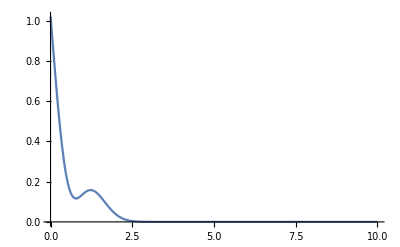

```mathematica
Plot[testf,{x,0,10},PlotRange->All]
```

```mathematica
q=10
```

10

```mathematica
coeffspr=((testf*N[p,32]*Exp[x^2])/.x->nodes[[q*(q-1)/2+1;;q*(q-1)/2+q]]).gaussweights[[q*(q-1)/2+1;;q*(q-1)/2+q]]
```

{0.752698,0.527015,0.124424,-0.209071,0.00851262,0.0353623,-0.00571536,-0.00347392,0.000908231,0.000228767,0.}

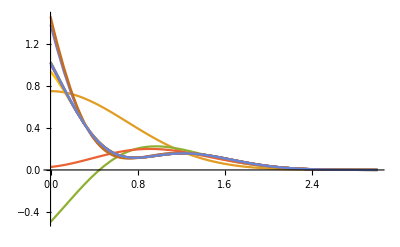

```mathematica
Plot[{testf,Evaluate[Table[Exp[-x^2]*HornerForm[coeffspr[[1;;k]].p[[1;;k]]],{k,1,kmax, 1}]]},{x,0,3},PlotRange->All]
```